```mathematica
ode=ψ'[x]+(x+(1+3 x^2)/(1+x+x^3))ψ[x]-x^3-2x-x^2(1+3 x^2)/(1+x+x^3)==0
```

-2 x-x^3-(x^2 (1+3 x^2))/(1+x+x^3)+(x+(1+3 x^2)/(1+x+x^3)) ψ[x]+ψ'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,ψ[x],x]]
```

{{ψ[x]→x^2+(ⅇ^(-x^2/2) C[1])/(1+x+x^3)}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,ψ[0]==1},ψ[x],x]]
```

{{ψ[x]→x^2+(ⅇ^(-x^2/2))/(1+x+x^3)}}

```mathematica
ψa[x_]:=ψ[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ψa[x],x]]
```

2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)

```mathematica
dψadx[x_]:=2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)
```

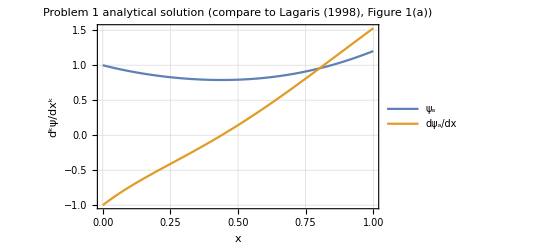

```mathematica
Plot[{ψa[x],dψadx[x]},{x,0,1},AxesLabel->{"x","d^kψ/dx^k"},PlotLegends->{"ψ_a","dψ_a/dx"},PlotLabel->"Problem 1 analytical solution (compare to Lagaris (1998), Figure 1(a))",Frame->True,GridLines->Automatic]
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
s1=NDSolve[{ode,ψ[0]==1},ψ[x],{x,0,1}]
```

{{ψ[x]→InterpolatingFunction[…][x]}}

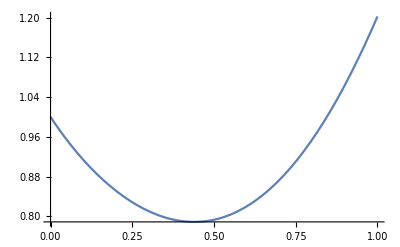

```mathematica
Plot[Evaluate[ψ[x]/.s1],{x,0,1}]
```

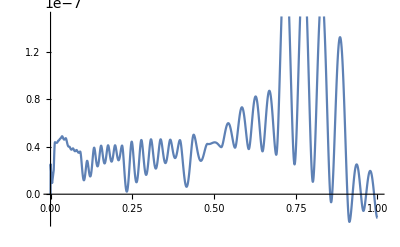

```mathematica
Plot[Evaluate[ψ[x]/.s1]-ψa[x],{x,0,1}]
```